Q=M M^T
Λ,V=eig(Q)
y=H(σ)
(∂ y)/(∂ M_(s t))=(∂ y)/(∂ λ_j)(∂ λ_j)/(∂ Q_(k l))(∂ Q_(k l))/(∂ M_(s t))
(∂ y)/(∂ M_(s t))=(∂ y)/(∂ λ_j)(∂ λ_j)/(∂ Q_(k l))(∂ Q_(k l))/(∂ M_(s t))
H(λ)=∑_(i=1)^D 1/2 log(2π e λ_i)
(∂y)/(∂ λ_i)=1/(2 λ_i)
(∂ λ_j)/(∂ Q_(k l))=v_(j k)v_(j l)
Q_(k l)=∑_(i=1)^n M_(k i)M_(l i)
(∂ Q_(k l))/(∂ M_(s t))=δ_(k,s)M_(l t)+δ_(l,s)M_(k t)
(∂ y)/(∂ M_(s t))=1/(2 λ_i)v_(j k)v_(j l)(δ_(k,s)M_(l t)+δ_(l,s)M_(k t))
(∂ y)/(∂ M_(s t))=1/(2 λ_i)(v_(j s)v_(j l)M_(l t)+v_(j k)v_(j s)M_(k t))

(∂ y)/(∂ M_(s t))=1/λ_i v_(j s)(v_(j l)M_(l t)+v_(j k)M_(k t))
(∂ y)/(∂ M_(s t))=1/λ_i v_(j s)v_(j k)M_(k t)

k=((i-1)i)/2+j
(∂ M_(s t))/(∂ m_i)=δ_(((s-1)s)/2+t,i)+δ_(((t-1)t)/2+s,i)

f=U(x)
x=M·z + μ
(∂ f)/(∂ μ_i)=(∂ f)/(∂ x_j)(∂ x_j)/(∂ μ_i)=(∂ f)/(∂ x_i)
x_i=M_(i j)z_j+μ_i
(∂ x_i)/(∂ M_(s t))=(∂ (M_(i j)z_j+μ_i))/(∂ M_(s t))=δ_(i,s)δ_(j,t)z_j=δ_(i,s)z_t
(∂ f)/(∂ M_(s t))=(∂ f)/(∂ x_i)(∂ x_i)/(∂ M_(s t))=(∂ f)/(∂ x_i)δ_(i,s)z_t=(∂ f)/(∂ x_s)z_t

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
<<"bbvi`";
```

```mathematica
ρ=.99;
Σ0={{1,ρ},{ρ,1}};
μ0={1,2};
U[x_,y_]=1/2({x,y}-μ0).LinearSolve[Σ0,({x,y}-μ0)];
Uq[x_,y_]=N[D1[U[x,y],{x,y}]];
```

```mathematica
Dim=2;
ITERATIONS=2^10;
STEPSIZE=0.005;
SAMPLES=20;
```

```mathematica
xs=gd1[U,Uq,Dim,{}];
```

102

204

306

408

510

612

714

816

918

1020

```mathematica
xs//Dimensions
```

{1024,5}

```mathematica
ps={};
For[i=1,i<=Log2[Length[xs]],i++,
(*Print[xs[[2^i,;;]]];*)
μ=xs[[2^i,1;;2]];Σ=MatrixPower[m2M[xs[[2^i,3;;]]],2];AppendTo[ps,ParametricPlot[μ+{Sqrt[Eigenvalues[Σ]][[1]] Cos[t],Sqrt[Eigenvalues[Σ]][[2]] Sin[t]}.RotationMatrix[-ArcTan@@Eigenvectors[Σ][[1]]],{t,0,2 π},PlotStyle->Directive[Dashed,Yellow],Frame->True,AspectRatio->Automatic,PlotRange->All]]];
```

```mathematica
μ=μ0;
Σ=Σ0;
AppendTo[ps,ParametricPlot[μ+{Sqrt[Eigenvalues[Σ]][[1]] Cos[t],Sqrt[Eigenvalues[Σ]][[2]] Sin[t]}.RotationMatrix[-ArcTan@@Eigenvectors[Σ][[1]]],{t,0,2 π},PlotStyle->Directive[Opacity[.5],Black],Frame->True,AspectRatio->Automatic,PlotRange->All]];
```

```mathematica
μ=xs[[-1,1;;2]];
Σ=MatrixPower[m2M[xs[[-1,3;;]]],2];
AppendTo[ps,ParametricPlot[μ+{Sqrt[Eigenvalues[Σ]][[1]] Cos[t],Sqrt[Eigenvalues[Σ]][[2]] Sin[t]}.RotationMatrix[-ArcTan@@Eigenvectors[Σ][[1]]],{t,0,2 π},PlotStyle->Directive[Dashed,Blue],Frame->True,AspectRatio->Automatic,PlotRange->All]];
```

```mathematica
μ=xs[[1,1;;2]];
Σ=MatrixPower[m2M[xs[[1,3;;]]],2];
AppendTo[ps,ParametricPlot[μ+{Sqrt[Eigenvalues[Σ]][[1]] Cos[t],Sqrt[Eigenvalues[Σ]][[2]] Sin[t]}.RotationMatrix[-ArcTan@@Eigenvectors[Σ][[1]]],{t,0,2 π},PlotStyle->Directive[Dashed,Red],Frame->True,AspectRatio->Automatic,PlotRange->All]];
```

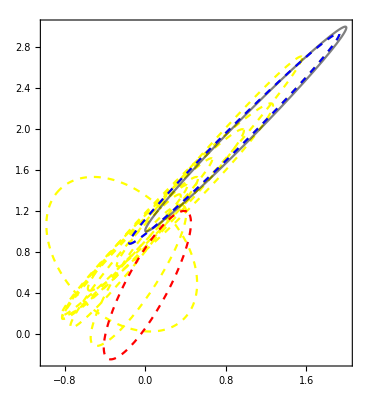

```mathematica
Apply[Show,ps]
```